Si può automatizzare la ricerca della biforcazione. Per determinare la biforcazione n-esima, si parte da un appropriato valore di μ inferiore a quello di biforcazione (stimato ad occhio) e si confrontano, per un N opportunamente grande, le iterate N-esima e (N+2^n)-esima di uno stesso punto inziale. Se sono molto vicini, non siamo ancora alla biforcazione, e bisogna aumentare μ. Appena cominciano ad allontanarsi, siamo arrivati alla biforcazione.

```mathematica
ClearAll["Global`*"]
```

```mathematica
f[μ_,x_]:= μ x(1-x)
fn[μ_,x_,n_]:=Nest[f[μ,#]&,x,n]
dist[μ_,x0_,Ν_,n_]:=Abs[fn[μ,x0,Ν]-fn[μ,x0,Ν+2^n]]
indagine[n_,x0_,Ν_,{min_,max_,step_}]:=ParallelTable[{μ,dist[μ,x0,Ν,n]},{μ,min,max,step}]
indaginePlot[n_,x0_,Ν_,{min_,max_,step_}]:=ListPlot[indagine[n,x0,Ν,{min,max,step}],AspectRatio->1,PlotRange->Full]
sospetto[n_,x0_,Ν_,{min_,max_,step_}]:=Module[
{
ind=indagine[n,x0,Ν,{min,max,step}],
val,
spike
},
val=Last/@ind;
spike=Max@val;
Cases[ind,{_,spike}]
]
```

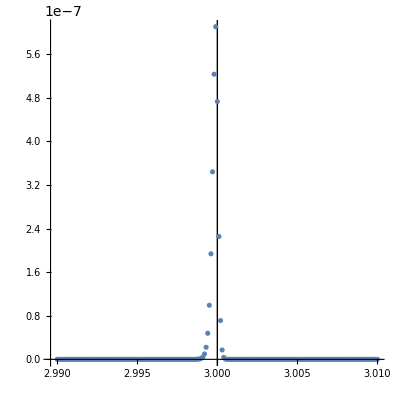

```mathematica
ListPlot[indagine[2,0.4,10^4,{2.99,3.01,10^-4}],AspectRatio->1,PlotRange->Full,Epilog->{InfiniteLine[{{3,0},{3,1}}]}]
```

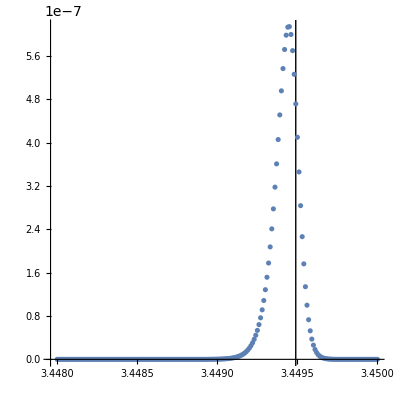

```mathematica
ListPlot[indagine[3,0.4,10^4,{3.448,3.45,10^-5}],AspectRatio->1,PlotRange->Full,Epilog->{InfiniteLine[{{1+√6,0},{1+√6,1}}]}]
```

```mathematica
(1+√6-3.4494459999999996)/(1+√6)
```

0.0000126809

Quindi non solo il metodo pare funzionare, ma gli errori numerici che compie potrebbero essere inferiori all’1%! Godo.

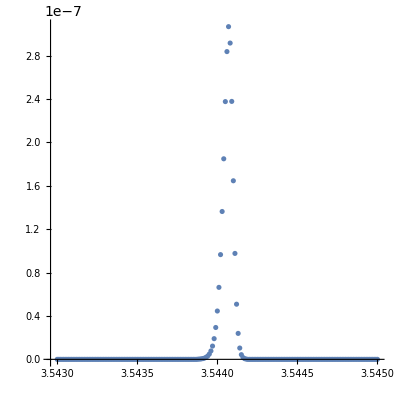

```mathematica
ListPlot[indagine[4,0.4,10^4,{3.543,3.545,10^-5}],AspectRatio->1,PlotRange->Full]
```

```mathematica
sospetto[4,0.4,10^4,{3.54,3.55,10^-5}]
```

{{3.54407,3.06786×10^-7}}

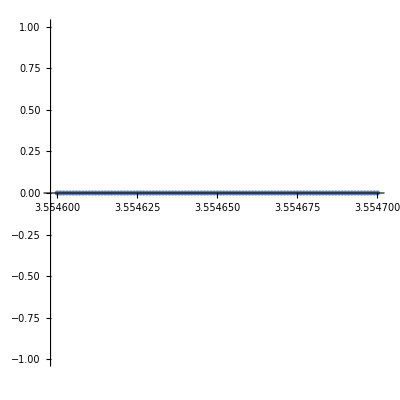

```mathematica
indaginePlot[5,0.4,10^6,{3.5546,3.5547,10^-6}]
```

```mathematica
NonlinearModelFit[Transpose[{Range[0,8],{1,3,1+√6,3.5440903,3.5644073,3.5687594,3.5696916,3.5698913,3.5699340}}],-Exp[b x]+c,{b,c},x]
```

FittedModel[3.34828-ⅇ^(-1.47075 x)]

```mathematica
Interpolation[Transpose[{Range[0,8],{1,3,1+√6,3.5440903,3.5644073,3.5687594,3.5696916,3.5698913,3.5699340}}]]
```

InterpolatingFunction[…]

```mathematica
Manipulate[Plot[{3.5699456718709449018420051513864989367638369115148323781079755299213628875001367775263210342163-2.853 ⅇ^(-α x)},{x,1,10},PlotRange->Full,Epilog->{Thick,Point/@({Range[8],{3,1+√6,3.5440903,3.5644073,3.5687594,3.5696916,3.5698913,3.5699340}}ᵀ)}],{α,1.5,1.6}]
```

```mathematica
Log[2.853 ]
```

1.04837

```mathematica
g[x_]:=3.5699456718709449018420051513864989367638369115148323781079755299213628875001367775263210342163-28530/10000 ⅇ^(-1.5409880955x);
NumberForm[Limit[(g[n-1]-g[n-2])/(g[n]-g[n-1]),n->Infinity],20]
```

4.669201609490461

```mathematica
(g/@Range[8]-{3,1+√6,3.5440903,3.5644073,3.5687594,3.5696916,3.5698913,3.5699340})/{3,1+√6,3.5440903,3.5644073,3.5687594,3.5696916,3.5698913,3.5699340}//Abs//Log10
```

{-1.8635,-2.52043,-3.21275,-3.88536,-4.55567,-5.2252,-5.89043,-6.5718}

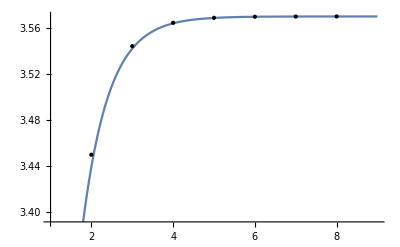

```mathematica
Plot[g[x],{x,1,9},Epilog->{Thick,Point/@({Range[8],{3,1+√6,3.5440903,3.5644073,3.5687594,3.5696916,3.5698913,3.5699340}}ᵀ)}]
```